## Exponente de Lyapunov

Es una medida de la divergencia entre dos trayectorias infinitesimalmente cercanas. Se supone que las trayectorias divergen de manera exponencia, de manera que si ϵ_0 es la separación entre dos puntos iniciales, la separación después de n iteraciones será

ϵ_n = ϵ_0 ⅇ^(n λ),

donde λ es el exponente de Lyapunov. Este se obtiene por medio de

λ = 1/n ∑_(k=0)^(n-1) ln|f'(x_k)|.

Si λ < 0 la órbita tiende hacia algún valor, si λ > 0 la órbita diverge.

Definición para mapeos unidimensionales

```mathematica
Lyapunov[f_,param_,x0_,iter_]:=Module[{n,pts},
n = iter;
pts = NestList[f[param,#]&,x0,iter];
Return[1/n Sum[Log[Abs[D[f[param,x],x]/. x-> i]],{i,pts}]];
];
LyapunovNum[f_,param_,x0_,iter_,eps_]:=Module[{n,pts,x,xeps,sum,d},
n = iter;
x = x0;
xeps = x-eps;
sum = 0;
Do[
x = f[param,x];
xeps = f[param,xeps];
d = Abs[x-xeps];
sum += Log[d/eps];
xeps = x-eps;,
{iter}
];
Return[sum/iter];
];
```

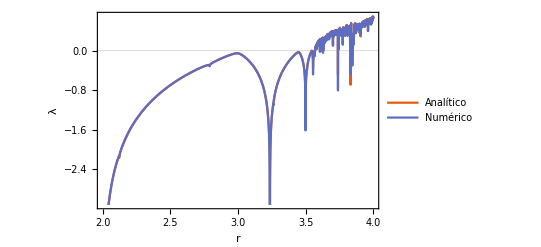

```mathematica
logisticmap[r_,x_]:= r x (1-x);
SetOptions[{Plot},BaseStyle->FontSize->14];
Print[Plot[{Lyapunov[logisticmap,r,0.234,100],LyapunovNum[logisticmap,r,0.234,100,0.0005]},{r,2,4},PlotTheme->"Scientific",PlotLegends->{"Analítico", "Numérico"},FrameLabel->{"r","λ"}]]
```

Definición para mapeos bidimensionales

Sea un sistema de ecuaciones
x_(t+1) = f_1(x_t,y_t),   y_(t+1) = f_2(x_t,y_t),

el exponente bidimensional de Lyapunov está dado por

λ = Lim_(T→ ∞) 1/T Log(|u_T|+|v_T|),

donde
u_(t+1) = (∂f_1)/(∂ x)u_t + (∂ f_1)/(∂ y) v_t, 
v_(t+1) = (∂f_2)/(∂ x)u_t + (∂ f_2)/(∂ y) v_t.

Definición para el mapa de Henón

```mathematica
f1[x_,y_,a_]:= 1+y-a x^2;
f2[x_,b_]:= b x;
vf1[xs_,ys_,a_,b_,u_,v_]:= (D[f1[x,y,a], x] u + D[f1[x,y,a], y] v)/. {x-> xs, y-> ys};
vf2[xs_,b_,u_,v_]:= (D[f2[x,b], x] u + D[f2[x,b], y] v) /. x-> xs;

henonpts[a_,b_,pts_] := NestList[{f1[#[[1]],#[[2]],a], f2[#[[1]],b]}&,{0.1,0.3},pts];
lyapunov[a_,b_,pts_] := Module[{henoncoords,uv},
henoncoords = henonpts[a,b,pts];
uv = Nest[{#[[1]]+1, vf1[henoncoords[[#[[1]],1]], henoncoords[[#[[1]],2]], a,b,#[[2]],#[[3]]], vf2[henoncoords[[#[[1]],1]], b,#[[2]],#[[3]]]}&,{1,0.5,0.5},pts];
Return[1/pts Log[Abs[uv[[1]]] + Abs[uv[[2]]]]];
];
```

```mathematica
data = Flatten[Table[{a,b,lyapunov[a,b,1000]},{a,0.5,1.42,0.1},{b,0.2,0.31,0.01}],1];
SetOptions[{Histogram,Plot,ListPlot,ListPlot3D},BaseStyle->FontSize->14];
ListPlot3D[data, AxesLabel->{"a","b", "λ"},PlotStyle->PointSize[Large]]
```

-Graphics3D-